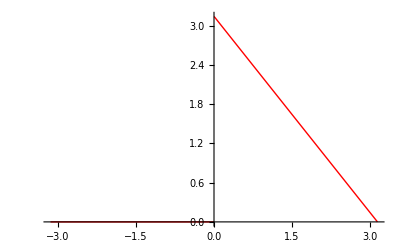

```mathematica
Plot[Piecewise[{{0,x<0},{Pi - x,x>0}}],{x,-Pi,Pi}, PlotStyle->{Thick, Red}]
```

```mathematica
f[x_]=Piecewise[{{0,x<0},{Pi - x,x>0}}]
```

Piecewise[{{0, x<0}, {π-x, x>0}, {0, True}}]

```mathematica
S1 = FourierSeries[f[x],x,1];
S5 = FourierSeries[f[x],x,5];
S10 = FourierSeries[f[x],x,10];
S100 = FourierSeries[f[x],x,100];
PS1 = Plot[{f[x],S1},{x,-Pi,Pi}, PlotStyle->{Red, Blue},PlotLegends->Placed[{Subscript["S",1], "f(t)"},Top]];
PS5 = Plot[{f[x],S5},{x,-Pi,Pi}, PlotStyle->{Red, Blue},PlotLegends->Placed[{Subscript["S",5], "f(t)"},Top]];
PS10 = Plot[{f[x],S10},{x,-Pi,Pi}, PlotStyle->{Red, Blue},PlotLegends->Placed[{Subscript["S",10], "f(t)"},Top]];
PS100 = Plot[{f[x],S100},{x,-Pi,Pi}, PlotStyle->{Red, Blue},PlotLegends->Placed[{Subscript["S",100], "f(t)"},Top]];
```

```mathematica
GraphicsGrid[{{PS1,PS5},{PS10,PS100}}]
```

-Graphics-